```mathematica
psiseries[x_,y_,m_,l_]:=Sum[(-1)^j*(2j + 1)*y^(2j)*HurwitzZeta[2j + 2,x],{j, 0, m}] + y^2*Sum[((-1)^(m+1)*(2m+1)*y^(2m+2) + (-1)^(m+1)*(2m+3)*y^(2m)*(x + n)^2)/((x+n)^(2m+2)*((x+n)^2 + y^2)^2),{n,0,l}]
altseries[x_,y_,m_,l_]:=Sum[(-1)^j*(2j + 1)*y^(2j)*PolyGamma[2j + 1,x]/Factorial[2j + 1],{j, 0, m}] + y^2*Sum[((-1)^(m+1)*(2m+1)*y^(2m+2) + (-1)^(m+1)*(2m+3)*y^(2m)*(x + n)^2)/((x+n)^(2m+2)*((x+n)^2 + y^2)^2),{n,0,l}]
psishift[x_,y_,m_,l_] := If[x < 1,Re[1/(x + I*y)^2] + psiseries[x + 1, y, m, l], psiseries[x, y, m, l]]
altshift[x_,y_,m_,l_] := If[x < 1,Re[1/(x + I*y)^2] + altseries[x + 1, y, m, l], altseries[x, y, m, l]]
```

```mathematica
altseries[1,0.01,10,100]
```

1.64461

```mathematica
psiseries[1, 0.01, 10, 100]
psishift[1,0.01,10,100]
psishift[0.5,0.01,10,100]
Re[PolyGamma[1,1  + 0.01I]]
```

1.64461

1.64461

4.92993

1.64461

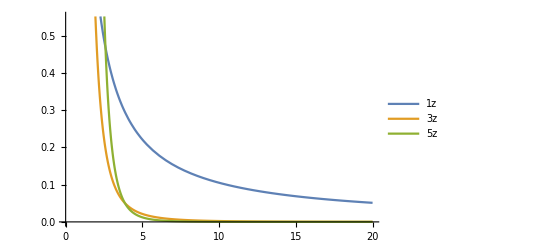

```mathematica
Plot[{PolyGamma[1,z],PolyGamma[3,z], PolyGamma[5,z]},{z, 0, 20},PlotLegends->"Expressions"]
```

```mathematica
Plot3D[Re[PolyGamma[1,x+I*y]],{x,0,1},{y,1,5},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[psishift[x,y,1,10],{x,0.01,1},{y,1,5},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[(Re[PolyGamma[1,x+I*y]] - psishift[x,y,10,20])/Re[PolyGamma[1,x+I*y]]],{x,0.01,1},{y,1,6}, PlotRange -> Full]
```

-Graphics3D-

```mathematica
Plot3D[Abs[(Re[PolyGamma[1,x+I*y]] - altshift[x,y,5,50])/Re[PolyGamma[1,x+I*y]]],{x,0.01,1},{y,1,6}, PlotRange -> Full]
```

$Aborted

```mathematica
PolyGamma[1, 0.0001+ I*5]
```

-0.0199961-0.198656 ⅈ